# Rapport Inlämningsuppgift 1, Projekt Grupp 17

Malcolm Liljedahl, IX1307, malcolml@kth.se
Ted Melander, IX1307, tedme@kth.se

Uppgift 1: Polynomekvation

## Uppgifter och Resultat

### Uppgift

Hitta lösningarna till polynomekvationen: x^5+23/3 x^4+25/3 x^3-107/3 x^2-148/3 x+20=0. 
Rita också grafen för polynomet och markera nollställen med en röd punkt.

### Resultat

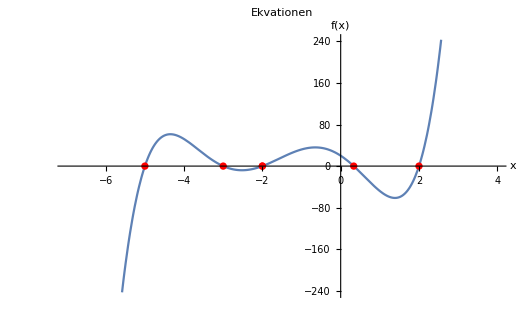

Lösningarna till funktionen är: {-5,-3,-2,1/3,2}.

## Kod

```mathematica
f[x_] = x^5+23/3 x^4+25/3 x^3-107/3 x^2-148/3 x+20
```

```mathematica
Plot[f[x], {x, -7, 3}, AxesLabel->{"x","f(x)"}]
```

Här illustreras funktionen f(x)i form av en graf:

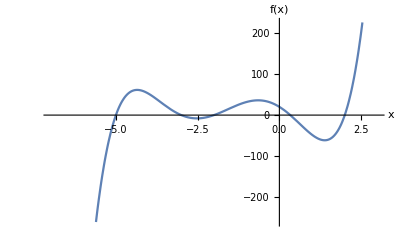

Här är funktionen f(x) nollställen:

```mathematica
{x1, x2, x3, x4, x5} = x/. Solve[f[x]==0, x]
```

{-5,-3,-2,1/3,2}

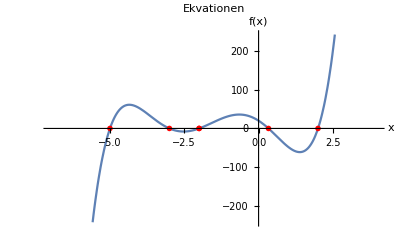

```mathematica
Plot[f[x],{x,-7,4},AxesLabel->{"x","f(x)"},PlotLabel->"Ekvationen ",Epilog->{PointSize[0.01],Red,Point[{{x1,f[x1]},{x2,f[x2]},{x3,f[x3]},{x3,f[x3]},{x4,f[x4]},{x5,f[x5]}}]}]
```

Här ovanför visas grafen med röd markerade nollställen.

Uppgift 2: Olikhet

## Uppgifter och Resultat

### Uppgifter

Lös uppgift 9 och 10 i filen Algebraiska likheter och olikheter med hjälp av Mathematica. I de fall det är lämpligt illustrera lösningsområdet grafiskt.

9. Lös följande olikheter i domänen av alla reella tal:

a)
x+2>6 x^2

b)
(x+1)/((x-2)(2x+3))≥0

c)
(x^2-5)/(x-1)≤-1

d)
-√(x^2 + 9)≥2√x+4

e)
√(3x+3)≥√x+1

10. Bestäm sanningsmängder till följande predikater i domänen av alla reella tal:

a)
x^3<1˄ x^2 - x - 6≥0

b)
(2x-1)(x-3)(2x-5) = 0 ˄ √(x^2 -x -2) ≥2

c)√(x^2-x-2)≥ √x ˄ x^2 -1 ≥ 0

### Resultat

9.

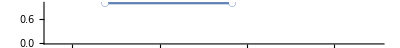
a) -1/2<x<2/3

Resultatet illustrerat på en tallinje:
-Graphics-

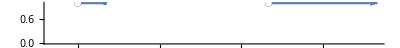
b) -3/2<x≤-1||x>2

Resultatet illustrerat på en tallinje:
-Graphics-

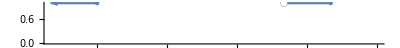
c) x≤-3 || 1 < x ≤ 2

Resultatet illustrerat på en tallinje:
-Graphics-

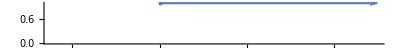
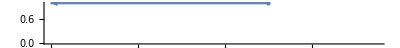
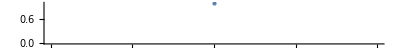
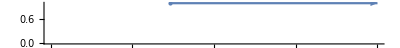
d) -√(x^2 + 9)≥2√x+4

False

Då den är False så har vi inget att illustrera med en tallinje. 


e) x≥0

Resultatet illustrerat på en tallinje:
-Graphics-

10.


a) x≤-2

Resultatet illustrerat på en tallinje:
-Graphics-


b) x=3

Resultatet illustrerat på en tallinje:
-Graphics-

c) x≥1+√3

Resultatet illustrerat på en tallinje:
-Graphics-

## Kod

9.

a)

```mathematica
Reduce[x+2>6 x^2, x]
```

-1/2<x<2/3

```mathematica
NumberLinePlot[2+x>6 x^2, {x,-1,2}]
```

-Graphics-

b)

```mathematica
Reduce[(x+1)/((x-2)(2x+3))≥0,x]
```

-3/2<x≤-1||x>2

```mathematica
NumberLinePlot[(x+1)/((x-2)(2x+3))≥0, {x,-2,4}]
```

-Graphics-

c)

```mathematica
Reduce[(x^2-5)/(x-1)≤-1,x]
```

x≤-3||1<x≤2

```mathematica
NumberLinePlot[(x^2-5)/(x-1)≤-1, {x,-4,3}]
```

-Graphics-

d)

```mathematica
Reduce[-√(x^2+9)≥2 √x+4,x]
```

False

e)

```mathematica
Reduce[√(3x+3)≥√x+1,x]
```

x≥0

```mathematica
NumberLinePlot[√(3x+3)≥√x+1, {x,-1, 2}]
```

-Graphics-

10.

a)

```mathematica
Reduce[ x^3<1&& x^2 - x - 6≥0]
```

x≤-2

```mathematica
NumberLinePlot[x≤-2, {x,-4,-1}]
```

-Graphics-

b)

```mathematica
Reduce[(2x-1)(x-3)(2x-5) == 0 ∧√(x^2 -x -2) ≥2]
```

x==3

```mathematica
NumberLinePlot[x==3, {x,2,4}]
```

-Graphics-

c)

```mathematica
Reduce[√(x^2-x-2)≥ √x ∧x^2 -1 ≥ 0]
```

x≥1+√3

```mathematica
NumberLinePlot[x≥1+√3, {x,2,4}]
```

-Graphics-

Uppgift 3: Binomisk Ekvation

## Uppgifter och Resultat

### Uppgifter

Finn lösningen till ekvationen z^6 = -3 + 3i och visa grafiskt att dessa ligger på en cirkel i komplexa
talplanet.

### Resultat

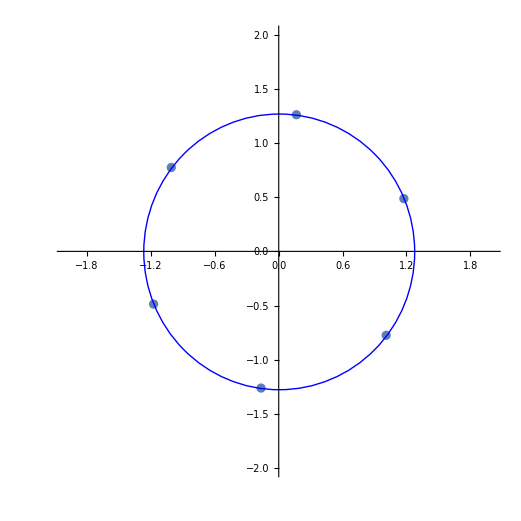
Här är dom komplexa punkterna i rektangulär form: {-1.1755-0.486907 ⅈ,1.1755+0.486907 ⅈ,-0.166075-1.26146 ⅈ,0.166075+1.26146 ⅈ,1.00942-0.774557 ⅈ,-1.00942+0.774557 ⅈ}

Tillsammans så bildar punkterna en cirkel i det komplex talplanet:

-Graphics-

## Kod

```mathematica
Z = z/. Solve[z^6 == -3 + 3I] //N
```

{-1.1755-0.486907 ⅈ,1.1755+0.486907 ⅈ,-0.166075-1.26146 ⅈ,0.166075+1.26146 ⅈ,1.00942-0.774557 ⅈ,-1.00942+0.774557 ⅈ}

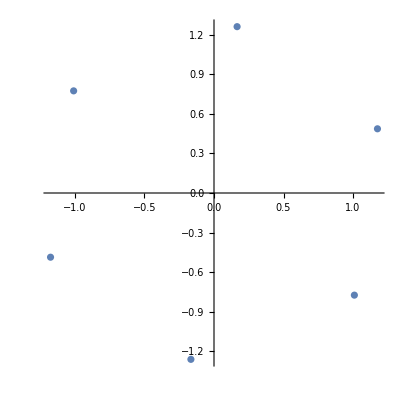

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@Z,AspectRatio->1]
```

Ovanför här är den graf som mathematica automatiskt föreslog. För att visa en tydligare cirkel så ändrar vi “PlotRange” samt så använder vi Epilog för att binda ihop punkterna.

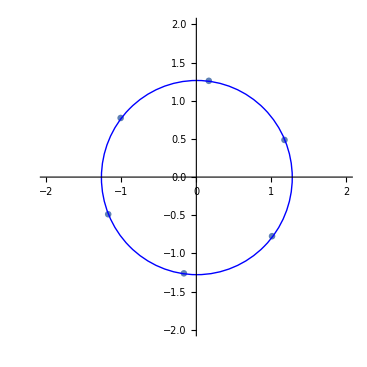

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@Z,AspectRatio->1, Epilog-> {Blue, Circle[{0,0}, Abs[Z[[1]]]]}, PlotRange-> {{-2,2},{-2,2}}]
```

Uppgift 4: Logik

## Uppgifter och Resultat

### Uppgifter

Lös uppgift 1b  i filen Logik med hjälp av Mathematica. 

1. Propositioner

Betrakta följande propositioner:
		p1:(√2∈R)∧∼(√2∈ Q)
		p2:1/2∈Z∨1/2∈Q
		p3: ∼(-4∈N)→ ∼(-4∈Z)
		p4: 2.5∈Q<-> 2.5∈R
		
		b) Vilka av dessa propositioner är sanna?

### Resultat

p1:(√2∈R)∧∼(√2∈ Q)
True

p2:1/2∈Z∨1/2∈Q
True

p3: ∼(-4∈N)→ ∼(-4∈Z)
True→False = False

p4: 2.5∈Q<-> 2.5∈R
True<->True = True

## Kod

Med hjälp av mathematicas “Element” så kan man bevisa vilka påståenden som är sanna eller falska.

Sedan i Fadil Galjics bok “MATEMATISK KOMMUNIKATION, ARGUMENTATION OCH SKAPANDE” så fick vi lära oss vad vilka domäner som använder vilka symboler.1
R=Reella tal=Reals
Q=Rationella tal=Rationals
Z=Heltal=Integers
N=Naturliga tal=NonNegativeIntergers2

p1:(√2∈R)∧∼(√2∈ Q)

```mathematica
Element[√2,Reals]∧NotElement[√2,Rationals]
```

True

p2:1/2∈Z∨1/2∈Q

```mathematica
Element[1/2, Integers]∨Element[1/2, Rationals]
```

True

p3: ∼(-4∈N)→ ∼(-4∈Z)

```mathematica
Not[Element[-4,  NonNegativeIntegers]]->Not[Element[-4, Integers]]
```

True→False

p4: 2.5∈Q<-> 2.5∈R

```mathematica
Element[2/5, Rationals]<->Element[2.5, Reals]
```

True<->True

Referenser till uppgift 4:

1	Fadil Galjic. MATEMATSIK KOMMUNIKATION, ARGUMENTATION OCH SKAPANDE. Lund: Studentlitteratur, 2020,10

2	https://mathworld.wolfram.com/NaturalNumber.html

Uppgift 5: Ekvationslösning och grafer

## Uppgifter och Resultat

### Uppgifter

En D’Artagnan jagas av Richeliue. Båda rider så snabbt de kan. D’Artagnan rider med en hastighet av 42 km/h och Richeliue med 57 km/h. Richeliue är 60 meter efter D’Artagnan och det är 250 meter till stadsporten där D’Artagnan kan komma undan. Bestäm om Richeliue hinner i kapp D’Artagnan och i så fall vilken tidpunkt och sträcka innan stadsporten det sker. Illustrera tidsförloppet grafiskt på lämpligt sätt.

### Resultat

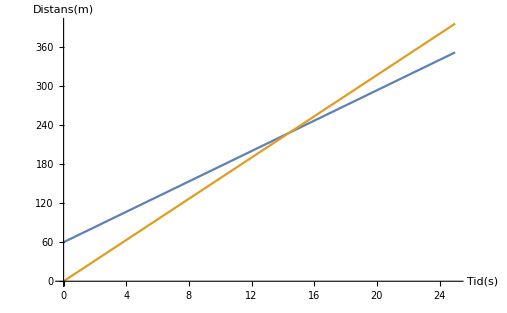
Via uträkningar så såg vi att D’Artagnan skulle nå fram till porten på 21,4 sekunder, medans Richeliue skulle nå fram till porten på 19,6 sekunder. Genom att skapa en funktion för varje utfall så kunde vi skapa en graf där vi sedan kunde se att Richeliue hinner ikapp D’Artagnan efter 14,4 sekunder.

Här är grafen:

-Graphics-

Svaret är rimligt. Då deras avståndsskillnad bara är 60meter men Richeliue kör konstant 15km/h snabbare(ingen accerelation är inräknad). Med uträkningar då så kunde vi se att Richeliue tar igen avståndsskillnaden på ca en 1sekund.

## Kod

För att skapa en lämplig demontration via en graf så använder vi sträcka(s) som y-axel och tid(t) som x-axel.

D’Artagnan: v(1) = 42km/h = 42000/3600 m/s, s(1) = 250m
Rícheliue: v(2) = 57km/h =57000/3600 m/s, s(2) = 250 + 60m

v=s/t→ t=s/v

Här deklareras de variabler som vi vill använda:

```mathematica
s1=250
```

250

```mathematica
v1=42000/3600
```

35/3

```mathematica
s2=250+60
```

310

```mathematica
v2=57000/3600
```

95/6

Här räknas tiden ut för sträckan D’Artagnan och Rícheliue åker med en given hastighet(detta görs för att se hur lång vår x-axel måste vara):

```mathematica
t1=s1/v1
```

150/7

```mathematica
t2=s2/v2
```

372/19

```mathematica
N[150/7]
```

21.4286

```mathematica
N[372/19]
```

19.5789

```mathematica
Quit[]
```

Då har vi nu all data vi behöver för att skapa våra funktioner och sedan våran graf.

v=s/t→ t=s/v→ s=v×t

```mathematica
v1=42000/3600
```

35/3

```mathematica
v2=57000/3600
```

95/6

```mathematica
s1[t_]:=v1×t + 60
```

```mathematica
s2[t_]:=v2×t
```

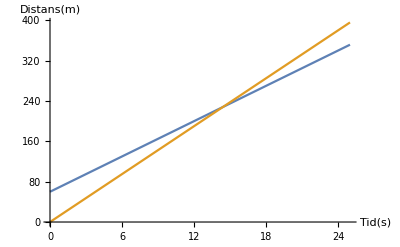

```mathematica
Plot[{s1[t],s2[t]},{t,0,25}, AxesLabel->{"Tid(s)","Distans(m)"}]
```

```mathematica
FindRoot[s1[t]==s2[t],{t,25}]
```

{t→14.4}

Tiden det tar för Richeliue att köra 60meter:

```mathematica
tR=sR/vR=60/57
```

20/19

```mathematica
N[20/19]
```

1.05263

Referenser

## Referenslista

Fadil Galjic. MATEMATSIK KOMMUNIKATION, ARGUMENTATION OCH SKAPANDE. Lund: Studentlitteratur, 2020

https://mathworld.wolfram.com/NaturalNumber.html

https://reference.wolfram.com/language/ref/FindRoot.html 

https://www.wolfram.com/language/fast-introduction-for-math-students/en/fractions-and-decimals/

Datorövning 1 dokument